## Homework 5

## Computational Exercise 1

1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1Original Relation

-Graphics-

1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1Symmetric Subelation

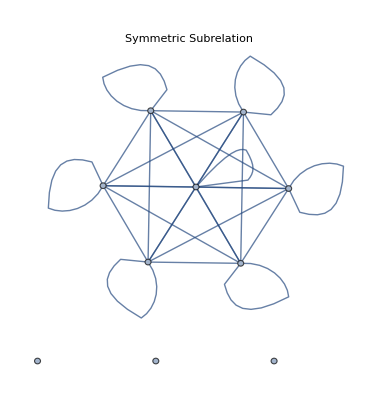

```mathematica
ClearAll[result]
subsym[x_] := Module[{result=Table[Table[0, Length[x]], Length[x]]},
Do[If[x[[i]][[j]] == 1 && x[[j]][[i]] == 1,
result[[i]][[j]] = 1,
0], {i, 1, Length[x]}, {j, 1, Length[x]}];
result
]
x = Table[{1,0,1,1,0,1,1,1,0,1}, 10];
x//Labeled[TableForm[#],"Original Relation"]&
AdjacencyGraph[x, PlotLabel->"Graph of original adjacency matrix"]
s = subsym[x];
s//Labeled[TableForm[#],"Symmetric Subelation"]&
AdjacencyGraph[s, PlotLabel->"Symmetric Subrelation"]
```

## Compuational Exercise 2

```mathematica
adjMatrix = Table[RandomChoice[{0, 1},5], 5]
adjMatrix//Labeled["Adjacency Matrix", TableForm[#]]&
adjGraph = AdjacencyGraph[adjMatrix, PlotLabel->"Adjacency Graph"]
```

{{1,0,1,1,0},{1,1,1,1,0},{0,0,0,1,1},{1,1,1,1,0},{0,0,1,0,0}}

Adjacency Matrix1 | 0 | 1 | 1 | 0
1 | 1 | 1 | 1 | 0
0 | 0 | 0 | 1 | 1
1 | 1 | 1 | 1 | 0
0 | 0 | 1 | 0 | 0

-Graphics-

```mathematica
StringForm["Is the relation reflexive? ``", AllTrue[Diagonal[adjMatrix], # == 1 &]]
symmetric[x_] := Module[{},
Do[
If
[x[[i]][[j]] == 1 && x[[j]][[i]]  == 0 ,
Return[False]
];
Return[True], 
{i, 1, Length[x]}, 
{j, 1, Length[x]}
]
]
StringForm["Is the relation symmetric? ``", symmetric[adjMatrix]]
```

Is the relation reflexive? False

Is the relation symmetric? True

```mathematica
reflexivize[x_]:= Module[{result = x}, 
Do[
result[[i]][[i]]=1, 
{i, 1, Length[x]}];
Return[result]]
reflexiveAdjMatrix = reflexivize[adjMatrix];
StringForm["Is the new relation (with reflexive closure) reflexive? ``", AllTrue[Diagonal[reflexiveAdjMatrix], # == 1 &]]
AdjacencyGraph[reflexiveAdjMatrix]
```

Is the new relation (with reflexive closure) reflexive? True

-Graphics-

Is the new relation (with symmtric closure)? True

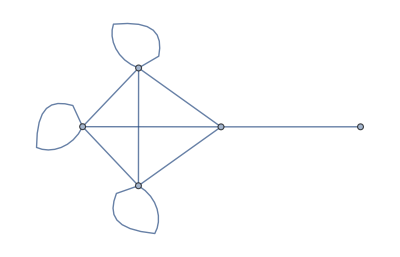

```mathematica
symmetrize[x_]:=Module[{result=x}, Do[
If[result[[i]][[j]] == 1, result[[j]][[i]] =1, ],
{i, 1, Length[result]}, {j, 1, Length[result]}];
Return[result]]
symmetricAdjMatrix = symmetrize[adjMatrix] ;
StringForm["Is the new relation (with symmtric closure)? ``", symmetric[symmetricAdjMatrix]]
AdjacencyGraph[symmetricAdjMatrix]
```